## ГЛАВА1. Основы работы в системе Mathematica

### 1.1 Структура Mathematica

Mathematica состоит из двух основных частей - ядра (kernel), производящего  вычисления по заданным командам, и интерфейсного процессора (front end), задающего внешнее оформление и характер взаимодействия с пользователем и системой. Вся работа осуществляется в окне рабочего документа - блокнота (notebook), - внешний вид которого зависит от типа платформы и определяется интерфейсным процессором, своим для каждой платформы. Блокнот может содержать различные математические и специальные символы, графические объекты, однако внутреннее представление документа, с которым работает ядро программы, - всегда  неформатированный текст. Это позволяет легко переносить документы с одной платформы на другую.

### 1.2 Предварительная информация о встроенной справочной системе

LЫ i ш c і e х n э c ч e ш џ      C$M$0$0$0$1$-$2$2$0$7$2$0$0$2

#### Использование ядра

Справочные средства ядра вызываются командами ? и ??. Для получения информации о любом объекте, известном ядру системы, следует выполнить команду ?<имя объекта>. Например, выведем информацию о встроенной константе Pi :

```mathematica
?Pi
```

Pi is π, with numerical value ≃3.14159.

Для вывода более подробной информации используется ?? :

```mathematica
??Pi
```

Pi is π, with numerical value ≃3.14159.

Attributes[π]={Constant,Protected,ReadProtected}

Кроме того, при выполнении команды ? возможно использование шаблона - символа * в имени объекта:

```mathematica
?*Plot*
```

RowBox[{"VectorPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a vector plot of the vector field RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"VectorPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several vector fields. 
RowBox[{"VectorPlot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variables RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}] to be in the geometric region StyleBox["reg", "TI"].

System`
ContourPlot | ListPlot | Plot | PlotJoined
DensityPlot | ListPlot3D | Plot3D | PlotLabel
ListContourPlot | ParametricPlot | Plot3Matrix | PlotPoints
ListDensityPlot | ParametricPlot3D | PlotDivision | PlotRange

Многие встроенные функции и команды в Mathematica имеют необязательные дополнительные параметры - опции. Вывести список всех опций той или иной функции, а также их значения по умолчанию позволяет команда Options[] :

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

### 1.3 Арифметические операции и их последовательность

Начнем работу в Mathematica с основных арифметических операций.

```mathematica
2+2
```

4

При первом вычислении загружается ядро Mathematica, которое производит все вычисления.
После того как ядро запущено попробуем сложить два 32-х разрядных числа

```mathematica
25011975435874958739485752161534+93582954263219754871911197685729
```

118594929699094713611396949847263

На этот раз результат появляется практически мгновенно.

expr1 + expr2 + ... + exprn  или Plus[expr1, expr2,..., exprn]
сложение выражений expr1, expr2, ..., exprn.

"Усложним" задачу и вставим в середину каждого из слагаемых знак вычитания:

```mathematica
2501197543587495-8739485752161534+9358295426321975-4871911197685729
```

-1751903979937793

expr1 - expr2  или  Subtract[expr1, expr2], а также
expr1 - expr2 - ... - exprn 
вычитание выражений.

- expr  или  Minus[expr]
изменить знак выражения expr.

Теперь разобьем все числа знаком умножения (пробел или *):

```mathematica
25011975 43587495-87394857 52161534+93582954 26321975-48719111 97685729
```

-5764314168230782

Обратите внимание, что в Mathematica умножение имеет привычный приоритет над сложением и вычитанием.

expr1  expr2  ...  exprn  или  Times[expr1, expr2,..., exprn]
вычисление произведения выражений expr1, expr2, ..., exprn.

Далее вставим в середину каждого числа знак деления:

```mathematica
2501/1975 4358/7495-8739/4857 5216/1534+9358/2954 2632/1975-4871/9111 9768/5729
```

-139784933181959569928678/67481856082797296274875

Здесь следует отметить, что в Mathematica деление имеет приоритет над умножением, хотя в данном случае это не оказывает влияния на итоговый результат.

expr1 / expr2  или  Divide[expr1, expr2]
деление выражений.

Наконец, лишим последнего шанса тех, кто решил вручную проверить правильность компьютерных вычислений, — в середину каждого числа добавим знак возведения в степень:

```mathematica
25^01/19^75 43^58/74^95-87^39/48^57 52^16/15^34+93^58/29^54 26^32/19^75-48^71/91^11 97^68/57^29
```

-(95625838569430126051863553949740902204554617817902954610132215940631391074770036302317933539971726857636689884307129166127322329467946802707360843083603329259541047723773471793699302239160376039560023234765109334106372213484550610823924135372487548037408338744459326112002307136010810527779649222827234064601774079513254038509632147597557599967688851845233202941076729679945988460599682826654385685065130846348076468463910484712538940000429687132394080272614847047912261756513430008718145746740075423734049557830549755819035309485670958955516732461317969994768404148513955346014260242855793944553923115313429029367118702394032891495113/958949203772924534127533842593529337200049829111198472305366735483593814431425298546817888010827413448995817247137720484385257483262823938061951729084389215764978786144763208276575420652609499879458172906760207734939235401259356736524707235522818202893073634398829806059270620784965711572918944824823034649143673971894392500674962667703616235882238285411686304978833230854813117382941669228395292928225370138745063342080000000000000000000000000000000000)

И в данном случае отметим, что возведение в степень имеет приоритет по отношению ко всем другим арифметическим операциям.

expr1 ^ expr2 ^ ... ^ exprn  или Power[expr1, expr2,..., exprn]
возведение выражений в степень.

Для изменения принятого порядка осуществления арифметических операций естественным образом используются круглые скобки.

### 1.4 Точные и приближенные вычисления

Все вычисления Mathematica по умолчанию производит точно:

```mathematica
(3/4)^(3333/70)
```

(26588814358957503287787 3^(43/70))/(39614081257132168796771975168 2^(8/35))

```mathematica
%^(70/3333)
```

3/4

Здесь знак % означает результат предыдущей операции. Вообще, выполняя небольшие по объему вычисления "на скорую руку", можно использовать символы %, %%, %%% для обращения к результатам команд, выполненных один, два или три шага назад, соответственно. Запись %n (или Out[n]) заменяет результат, находящийся в строке с меткой Out[n].
Для представления результата вычисления в виде числа с плавающей точкой используется команда N.

```mathematica
N[%%]
```

1.12495×10^-6

Эта команда по умолчанию выводит шесть значащих разрядов результата, из которых один — слева от десятичной точки, и необходимую степень 10. Командой N можно воспользоваться и для вывода большего количества знаков числа.

```mathematica
N[%%%,150]
```

1.12494502226821874375400743145175947389085801244825745598851545435499811377073446268230451249689874256658610901224676179978768269303558098974216243199×10^-6

N[expr]
вычисление приближенного значения выражения expr.

N[expr, n]
вычисление приближенного значения выражения c заданным количеством значащих цифр.

Еще один способ дать команду на приближенное вычисление — записать любой из операндов с десятичной точкой.

```mathematica
3.+2/3
```

3.66667

### 1.5 "Школьные" функции

Команда извлечения квадратного корня может быть записана в Mathematica тремя разными способами — с помощью функции Sqrt, возведением в степень 1/2 и с использованием стандартной палитры.

```mathematica
Sqrt[16]
16^(1/2)
√16
```

4

4

4

Следует обратить внимание, как Sqrt работает с квадратом символьной переменной в случаях, когда ее знак не определен и когда определен.

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
Sqrt[Abs[x]^2]
```

Abs[x]

Здесь Abs — функция модуля.

Sqrt[expr]
вычисление квадратного корня из выражения expr.

Abs[expr]
вычисление модуля выражения expr.

Mathematica различает заглавные и строчные буквы. Поэтому вызов встроенных команд (констант, директив и т. д.) необходимо осуществлять именно так, как это показано в примерах: название всегда с большой буквы, аргументы — в квадратных скобках.

Функция логарифма может вызываться с одним аргументом (натуральный логарифм) и с двумя (в этом случае первый аргумент — основание, по которому вычисляется логарифм второго аргумента).

```mathematica
Log[E^5]
```

5

```mathematica
Log[2,1024]
```

10

E — встроенная константа — основание натурального логарифма.

```mathematica
E-Exp[1]
```

0

Log[expr]
натуральный логарифм выражения expr.

Log[base, expr]
логарифм выражения expr по основанию base.

Exp[expr]
возведение числа e2,718281 в степень expr.

Кроме числа e в Mathematica определены и некоторые другие математические константы

Pi
число  π = 3,141592

### Задача 1.

Как узнать, что больше E^π или π^E?

LЫ i ш c і e х n э c ч e ш џ      C$M$0$0$0$1$-$2$2$0$7$2$0$0$2

Решение:

```mathematica
{E^Pi > Pi^E, Pi^E > E^Pi}
```

{True,False}

I
мнимая единица; комплексное число, квадрат которого равен -1

Infinity
константа, служащая для представления +∞.

Встроенная функция для вычисления факториала может вызываться двумя способами:

```mathematica
Factorial[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

Factorial[expr] или expr!
вычисление факториала выражения expr.

### Задача 2.

Вычислить π  с точностью до 50 знаков.

Решение:

```mathematica
N[π,50]//Timing
```

{0.,3.1415926535897932384626433832795028841971693993751}

### Задача 3.

Разложить на множители x^16-y^16.

Решение:

```mathematica
Factor[x^25-y^25]
```

(x-y) (x^4+x^3 y+x^2 y^2+x y^3+y^4) (x^20+x^15 y^5+x^10 y^10+x^5 y^15+y^20)

### 1.6 Тригонометрические функции

Mathematica располагает набором встроенных тригонометрических функций, аргумент которых по умолчанию считается заданным в радианах.

```mathematica
Sin[13Pi/5]
```

√(5/8+(√5)/8)

Для перевода значения аргумента в градусную меру используется уже упомянутая константа Degree или символ ° из соответствующей палитры.

```mathematica
Cos[30Degree]
Cos[30°]
```

(√3)/2

(√3)/2

Sin[x], Cos[x], Tan[x], Cot[x], Sec[x], Csc[x]
тригонометрические функции Mathematica.

Шести тригонометрическим функциям в Mathematica соответствуют шесть обратных тригонометрических функций.

Они вычисляются как аналитические продолжения соответствующих тригонометрических функций действительного переменного. То есть, например, функция ArcSin для вещественного числа из отрезка  возвращает только значение главной ветви из промежутка 
[-π/2;π/2 ].

```mathematica
ArcSin[0.4]
```

0.411517

Функция ArcTan может быть записана с двумя аргументами x и y. В этом случае ее результатом будет значение -i Ln(x + iy)/(√(x^2)+y^2), которое при вещественных x и y равно аргументу комплексного числа x +iy :

```mathematica
ArcTan[√3/2,1/2]
ArcTan[-√3/2,-1/2]
```

π/6

-(5 π)/6

Знак ; на конце введенного выражения отменяет вывод результата вычисления на экран.
Ниже приведен код программы для изображения найденных углов.

{FontSize→14}

1/2

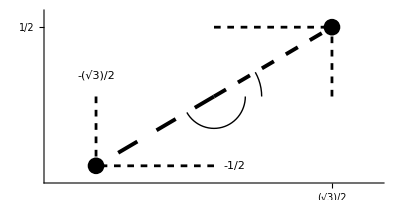

```mathematica
$TextStyle={FontSize->14}
x=√3/2;y=1/2
Show[Graphics[
{PointSize[0.03],
Point[{x,y}],Point[{-x,-y}],
{Thickness[.007],Dashing[{.025}],
Line[{{0,0},{x,y}}]},
{Thickness[.005],Dashing[{.012}],
Line[{{0,y},{x,y}}],
Line[{{0,-y},{-x,-y}}],
Line[{{x,0},{x,y}}],
Line[{{-x,0},{-x,-y}}]},
{Thickness[.007],Dashing[{.04}],
Line[{{0,0},{-x,-y}}]},
Circle[{0,0},0.35,{0,Pi/6}],
{Circle[{0,0},0.23,{-5Pi/6,0}]},{Text["-1/2",{.15,-1/2}],Text["-(√3)/2",{-(√3)/2,.15}]}         }],
Axes->True,AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-0.6,.6}},Ticks->{{{-√3/2,""},√3/2},{{-1/2,""},1/2}}]
Clear[x,y]
```

### 1.7 Некоторые команды аналитических преобразований

Введем произвольное алгебраическое выражение:

```mathematica
((b+a)^3+(a+b)^2)^2
```

((a+b)^2+(a+b)^3)^2

Единственное, что сделала Mathematica в данном случае, — это переписала выражение согласно собственным правилам. Для более существенного преобразования выражения дадим системе команду:

```mathematica
Expand[%]
```

a^4+2 a^5+a^6+4 a^3 b+10 a^4 b+6 a^5 b+6 a^2 b^2+20 a^3 b^2+15 a^4 b^2+4 a b^3+20 a^2 b^3+20 a^3 b^3+b^4+10 a b^4+15 a^2 b^4+2 b^5+6 a b^5+b^6

Как и следовало ожидать, функция Expand совершила действие, соответствующее значению этого английского слова, — раскрытие скобок. 
Следующая команда  переписывает выражение в виде произведения:

```mathematica
Factor[%]
```

(a+b)^4 (1+a+b)^2

Теперь введем рациональное выражение:

```mathematica
expr1=(1+a)^2/((2+a)(1-a))
```

(1+a)^2/((1-a) (2+a))

```mathematica
Expand[expr1]
```

1/((1-a) (2+a))+(2 a)/((1-a) (2+a))+a^2/((1-a) (2+a))

```mathematica
ExpandAll[expr1]
```

1/(2-a-a^2)+(2 a)/(2-a-a^2)+a^2/(2-a-a^2)

На этот раз скобок не осталось ни в числителе, ни в знаменателе. Однако все выражение в результате оказалось записано в виде суммы дробей. Переписать его более компактно поможет функция приведения к общему знаменателю.

```mathematica
Together[%]
```

(-1-2 a-a^2)/(-2+a+a^2)

Мы также можем попросить Mathematica выяснить, какая форма записи того или иного выражения является (с точки зрения системы) наиболее простой.

```mathematica
expr2=(a^4 x+2 a^3 b x-2 a b^3 x-b^4 x)/(a^3+a^2 b-a b^2-b^3)
```

(a^4 x+2 a^3 b x-2 a b^3 x-b^4 x)/(a^3+a^2 b-a b^2-b^3)

Знак ; на конце введенного выражения отменяет вывод результата вычисления на экран.

```mathematica
Simplify[expr2]
```

(a+b) x

Функция Simplify производит раскрытие скобок, ряд других алгебраических преобразований выражения и в итоге возвращает его наиболее простой вид. Кроме того, еще одним аргументом этой функции можно задать условия на переменные, входящие в упрощаемое выражение. Такими условиями могут служить уравнения, неравенства, указание принадлежности переменной к той или иной области числовых значений.

```mathematica
Clear[x];Simplify[x/(√(x^2))]
Simplify[x/(√(x^2)),x<0]
```

x/(√(x^2))

-1

Однако, примененная к выражениям со специальными функциями или c функциями комплексного аргумента, команда Simplify не всегда оказывается достаточно эффективной.

```mathematica
expr3=-1/2 I (1/2 Log[-1/2-I/2]^2-1/2 Log[-1/2+I/2]^2+1/2 (-(I π)/2+Log[2])^2-1/2 ((I π)/2+Log[2])^2)-1/2 I (I π Log[2]+Log[-1/2-I/2] Log[2]-Log[-1/2+I/2] Log[2]-1/2 I π Log[2-2 I]+Log[-1/2+I/2] Log[2-2 I]-1/2 I π Log[2+2 I]-Log[-1/2-I/2] Log[2+2 I])
```

-1/2 ⅈ (1/2 Log[-1/2-ⅈ/2]^2-1/2 Log[-1/2+ⅈ/2]^2+1/2 (-(ⅈ π)/2+Log[2])^2-1/2 ((ⅈ π)/2+Log[2])^2)-1/2 ⅈ (ⅈ π Log[2]+Log[-1/2-ⅈ/2] Log[2]-Log[-1/2+ⅈ/2] Log[2]-1/2 ⅈ π Log[2-2 ⅈ]+Log[-1/2+ⅈ/2] Log[2-2 ⅈ]-1/2 ⅈ π Log[2+2 ⅈ]-Log[-1/2-ⅈ/2] Log[2+2 ⅈ])

```mathematica
Simplify[expr3]
```

-1/4 ⅈ (Log[-1/2-ⅈ/2]^2-Log[-1/2+ⅈ/2] (Log[-2+2 ⅈ]-2 Log[2-2 ⅈ])-ⅈ π (Log[2-2 ⅈ]+Log[2+2 ⅈ])+Log[-1/2-ⅈ/2] (-2 Log[2+2 ⅈ]+Log[4]))

### Задача 9.

Упростить выражение a^3+b^3+c^3-3abc при условии a+b+c=0.

Решение:

```mathematica
Clear[a,b,c]
```

```mathematica
Simplify[a^3+b^3+c^3-3a b c,a+b+c==0]
```

0

Применение функции Factor (функция раскладывает на множители) демонстрирует правильность работы Simplify.

```mathematica
Factor[a^3+b^3+c^3-3a b c]
```

(a+b+c) (a^2-a b+b^2-a c-b c+c^2)

Еще раз убедимся в этом, используя уже функцию GroebnerBasis.

```mathematica
GroebnerBasis[{a^3+b^3+c^3-3a b c,a+b+c},{a,b,c}]
```

{a+b+c}

Ещё задача для команды Simplify:

```mathematica
Simplify[Cos[π n],n∈Integers]
```

(-1)^n

Более мощным инструментом упрощения выражений является функция FullSimplify.

```mathematica
FullSimplify[expr3]
```

1/8 π Log[2]

Часто, когда в некотором выражении необходимо заменить какую-либо переменную (или несколько переменных) конкретным числовым значением или целой формулой, используется команда ReplaceAll или ее сокращенная запись /. :

```mathematica
ReplaceAll[(Sin[x]*x^3+x^2*y+3Log[x y])/(x+y)^Cos[x/y],{x->3,y->a+b}]
```

(3+a+b)^(-Cos[3/(a+b)]) (9 (a+b)+3 Log[3 (a+b)]+27 Sin[3])

```mathematica
(3+a+b)^(-Cos[3/(a+b)]) (9 (a+b)+3 Log[3 (a+b)]+27 Sin[3])
```

(3+a+b)^(-Cos[3/(a+b)]) (9 (a+b)+3 Log[3 (a+b)]+27 Sin[3])

Первый аргумент команды ReplaceAll — преобразуемое выражение, второй — правило подстановки (или список таких правил), которое записывается в виде переменная -> выражение и определяет какую замену проводить. Заметим, что ReplaceAll подставляет вместо указанных переменных заданные выражения и позволяет увидеть результат, но исходное выражение не изменяет.

```mathematica
expr=x^2+4x+5
```

5+4 x+x^2

```mathematica
expr/.x->Sin[x]
```

5+4 Sin[x]+Sin[x]^2

```mathematica
expr
```

5+4 x+x^2

### 1.8 Команды организации списков

Список — важнейший тип данных в Mathematica. Именно с помощью списков представляются векторы и матрицы, а также структуры данных более высоких размерностей. 
Простейший одномерный список представляет собой различные выражения Mathematica, записанные в фигурных скобках через запятую:

```mathematica
{a, 2b, x^2+Sin[y], 78.896}
```

{a,2 b,x^2+Sin[y],78.896}

Пара фигурных скобок представляет собой краткую запись команды List. Поэтому определение списка можно произвести и следующим образом:

```mathematica
List[a, 2b, x^2+Sin[y], 78.896]
```

{a,2 b,x^2+Sin[y],78.896}

В Mathematica имеется ряд команд, позволяющих создавать списки автоматически. 
Команду Range используют, как правило, для создания списка, содержимое которого — последовательность чисел. Если аргумент команды Range — произвольное число k (не обязательно целое), то результатом будет список из натуральных чисел, не превосходящих k:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Вызванная с двумя аргументами k1 и k2, команда Range создает список чисел от k1 до k2 с шагом 1:

```mathematica
Range[3.8,10.5]
```

{3.8,4.8,5.8,6.8,7.8,8.8,9.8}

При этом k1 и k2 могут быть символьными выражениями, но их разность — обязательно числовым:

```mathematica
Range[a,a+7]
```

{a,1+a,2+a,3+a,4+a,5+a,6+a,7+a}

Если команда вызвана с тремя аргументами, то третий определяет величину шага:

```mathematica
Range[-1,1,0.4]
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

Допускается также одновременное задание нескольких списков:

```mathematica
Range[{1,3},{10,20},{2,3}]
```

{{1,3,5,7,9},{3,6,9,12,15,18}}

В этом случае созданные списки сами будут являться элементами списка.
Если элементы списка задаются по известному правилу (формуле), удобно использовать команду Table.

```mathematica
Table[(a+b)^i,{i,5}]
```

{a+b,(a+b)^2,(a+b)^3,(a+b)^4,(a+b)^5}

```mathematica
Table[2^i,{i,4,13}]
```

{16,32,64,128,256,512,1024,2048,4096,8192}

```mathematica
Table[Sin[i],{i,-Pi,Pi,.5}]
```

{-1.22465×10^-16,-0.479426,-0.841471,-0.997495,-0.909297,-0.598472,-0.14112,0.350783,0.756802,0.97753,0.958924,0.70554,0.279415}

Первым аргументом этой команды задается формула для создания элементов списка, включающая обычно некоторую переменную-счетчик (в данном случае i), которая для каждого элемента принимает определенное значение. Второй аргумент — итератор — определяет, в каких границах и с каким шагом счетчик должен изменяться. Итератор может включать от одного до четырех элементов, выполняющих те же функции, что и аргументы команды Range. Кроме того, может быть использовано несколько итераторов для формирования двумерных списков (матриц), а также списков более высоких размерностей:

```mathematica
lst=Table[i*j,{i,5},{j,5}]
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20},{5,10,15,20,25}}

```mathematica
%//MatrixForm
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

Для отображения двумерного списка в традиционном матричном виде применяется команда MatrixForm. В приведенном примере эта команда записана в постфиксной форме. В такой форме в Mathematica могут вызываться любые команды, которые употребляются с одним аргументом.
Обращение к отдельным элементам списка производится с помощью команды Part (альтернативная запись — [[ ]]).

```mathematica
Part[lst,2]
lst[[2]]
lst[[2,3]]
```

{2,4,6,8,10}

{2,4,6,8,10}

6

### Задача 20.

Исследовать основные команды (операторы) работы с матрицами.

```mathematica
Clear[MM,x,i,j,t,a]
```

Создаем матрицу.

```mathematica
MM=Table[x[i]^j,{i,1,3},{j,0,2}]
```

{{1,x[1],x[1]^2},{1,x[2],x[2]^2},{1,x[3],x[3]^2}}

Выводим ее в обычном виде.

```mathematica
MM//MatrixForm
```

(1 | x[1] | x[1]^2
1 | x[2] | x[2]^2
1 | x[3] | x[3]^2)

Вычисляем определитель.

```mathematica
Det[MM]//Simplify
```

-(x[1]-x[2]) (x[1]-x[3]) (x[2]-x[3])

Вачисляем обратную матрицу.

```mathematica
Simplify[Inverse[MM]]//MatrixForm
```

((x[2] x[3])/((x[1]-x[2]) (x[1]-x[3])) | -(x[1] x[3])/((x[1]-x[2]) (x[2]-x[3])) | (x[1] x[2])/((x[1]-x[3]) (x[2]-x[3]))
-(x[2]+x[3])/((x[1]-x[2]) (x[1]-x[3])) | (x[1]+x[3])/((x[1]-x[2]) (x[2]-x[3])) | (x[1]+x[2])/((x[1]-x[3]) (-x[2]+x[3]))
1/((x[1]-x[2]) (x[1]-x[3])) | -1/((x[1]-x[2]) (x[2]-x[3])) | 1/((x[1]-x[3]) (x[2]-x[3])))

Другая матрица и другая форма ввода.

```mathematica
MM={{a,1,0},{-1,a,1},{0,-1,a}}
```

{{a,1,0},{-1,a,1},{0,-1,a}}

```mathematica
MM//MatrixForm
```

(a | 1 | 0
-1 | a | 1
0 | -1 | a)

Собственные значения.

```mathematica
Eigenvalues[MM]
```

{a,-ⅈ √2+a,ⅈ √2+a}

Собственные векторы.

```mathematica
Eigenvectors[MM]
```

{{1,0,1},{-1,ⅈ √2,1},{-1,-ⅈ √2,1}}

Характеристический полином.

```mathematica
CharacteristicPolynomial[MM,t]
```

2 a+a^3-2 t-3 a^2 t+3 a t^2-t^3

Корни характеристического полинома.

```mathematica
Solve[2 a+a^3-2 t-3 a^2 t+3 a t^2-t^3==0,t]
```

{{t→a},{t→-ⅈ √2+a},{t→ⅈ √2+a}}

### Задача 21.

Из списка l={a,1,b,0,c,0,0,d} исключить все нулевые элементы.

Решение:

```mathematica
Clear[l,a,b,c,d]
```

```mathematica
l={a,1,b,0,c,0,0,d}
```

{a,1,b,0,c,0,0,d}

```mathematica
Delete[l,Position[l,0]]
```

{a,1,b,c,d}

### Задача 22.

Найти сумму отрицательных чисел в списке l={a,2,-1,b,c,-3}.

Решение:

```mathematica
Clear[l,a,b,c]
```

```mathematica
l={a,2,-1,b,c,-3}
```

{a,2,-1,b,c,-3}

```mathematica
Plus@@Select[l,Negative]
```

-4

### Задача 23.

Найти среднее квадратичное элементов списка l={-3,4,-7,0,11}.

Решение:

```mathematica
l={-3,4,-7,0,11}
```

{-3,4,-7,0,11}

```mathematica
√(∑_(i=1)^Length[l] l[[i]]^2)
```

√195

### Задача 24.

Преобразовать числовой список l в True, если в нем есть простые числа, или в False в противном случае.

Решение:

```mathematica
Clear[l]
```

```mathematica
l={6, 8 ,10,144,52}
```

{6,8,10,144,52}

```mathematica
Or@@PrimeQ/@l
```

False

```mathematica
l={6, 8 ,10,101,52}
```

{6,8,10,101,52}

```mathematica
Or@@PrimeQ/@l
```

True

### Задача 25.

Дана матрица M и столбец l. Как вставить l  k-м столбцом в матрицу?

Решение:

```mathematica
Clear[MM,l,k,a,b,c,d,f]
```

```mathematica
MatrInsert[M_,l_,k_]:=Transpose[Insert[Transpose[M],l,k]]
```

```mathematica
(M=Table[Random[Integer,{1,20}],{5},{5}])//MatrixForm
```

(17 | 1 | 13 | 3 | 8
3 | 19 | 17 | 6 | 19
14 | 13 | 17 | 1 | 20
2 | 19 | 17 | 13 | 1
7 | 16 | 5 | 19 | 10)

```mathematica
l={a,b ,c,d,f}
```

{a,b,c,d,f}

```mathematica
MatrInsert[M,l,2]//MatrixForm
```

(17 | a | 1 | 13 | 3 | 8
3 | b | 19 | 17 | 6 | 19
14 | c | 13 | 17 | 1 | 20
2 | d | 19 | 17 | 13 | 1
7 | f | 16 | 5 | 19 | 10)

```mathematica
MatrInsert[M,l,6]//MatrixForm
```

(17 | 1 | 13 | 3 | 8 | a
3 | 19 | 17 | 6 | 19 | b
14 | 13 | 17 | 1 | 20 | c
2 | 19 | 17 | 13 | 1 | d
7 | 16 | 5 | 19 | 10 | f)

### Задача 29.

Дан список переменных l={x,y,z} и список из значений m={1,2,3}. Получить список подстановок r={x→1,y→2,z→3}.

Решение:

```mathematica
Clear[l,m,x,y,z,a,b,c]
```

```mathematica
Subs[l_,m_]:=Thread[Rule[l,m]]
```

```mathematica
l={x,y,z}; m={1,2,3}
```

{1,2,3}

```mathematica
Subs[l,m]
```

{x→1,y→2,z→3}

```mathematica
Subs[l,{a,a+b,a+b+c}]
```

{x→a,y→a+b,z→a+b+c}

### 1.9 Некоторые функции математического анализа

Вычисление сумм, произведений, интегралов (определенных и неопределенных), производных (в том числе и частных), пределов функций и разложения в ряды Mathematica осуществляет как в числовой, так и в символьной форме.

Неопределенный интеграл:

```mathematica
Integrate[x/a^x,x]
```

-(a^-x (1+x Log[a]))/Log[a]^2

Определенный интеграл:

```mathematica
Integrate[x/Sin[x],{x,-1,1}]
```

1/2 ⅈ ((-2+π) π+4 ⅈ (ArcTanh[ⅇ^-ⅈ]+ArcTanh[ⅇ^ⅈ]+2 ⅈ PolyLog[2,ⅇ^ⅈ])+2 PolyLog[2,ⅇ^(2 ⅈ)])

В этом случае второй аргумент функции Integrate, содержащий информацию о переменной и пределах интегрирования, должен быть записан в виде списка.

Описанные функции интегрирования могут также быть вызваны нажатием соответствующей кнопки стандартной палитры:

```mathematica
∫_0^1 ((1-x)*Exp[x])/(1+x)ⅆx
```

(ⅇ-ⅇ^2-2 ExpIntegralEi[1]+2 ExpIntegralEi[2])/ⅇ

Для нахождения численного значения определенного интеграла используется функция NIntegrate:

```mathematica
NIntegrate[Cos[x]+Sin[Exp[x]],{x,0,Pi}]
```

0.644005

### Задача 5.

Найти интеграл ∫_a^b 1/(x-c)ⅆx, где a<c<b.

Интеграл существует только в смысле главного значения. Поэтому первоначально посмотрим существует ли соответствующая опция.

```mathematica
Options[Integrate]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
Integrate[1/(x-c),{x,a,b},PrincipalValue->True,Assumptions->{0<a,a<c,c<b}]
```

Log[(-b+c)/(a-c)]

Функция вычисления частных производных — одна из немногих, для обозначения которых использовано не полное английское слово. Вот, например, как вычисляется обычная производная выражения

(1+cos x)/(sin x)

```mathematica
D[(1+Cos[x])/Sin[x],x]
```

-1-(1+Cos[x]) Cot[x] Csc[x]

А в следующем примере вычисляется частная производная

∂^2/(∂x∂y^2)ln(x+y)cos^y y

```mathematica
D[Log[x+y]*Cos[x]^y,x,{y,2}]
```

(2 Cos[x]^y)/(x+y)^3-(2 Cos[x]^y Log[Cos[x]])/(x+y)^2+(Cos[x]^y Log[Cos[x]]^2)/(x+y)+(y Cos[x]^(-1+y) Sin[x])/(x+y)^2+(2 (-Cos[x]^(-1+y)-y Cos[x]^(-1+y) Log[Cos[x]]) Sin[x])/(x+y)+Log[x+y] (-2 Cos[x]^(-1+y) Log[Cos[x]]-y Cos[x]^(-1+y) Log[Cos[x]]^2) Sin[x]

Все элементы дифференцируемого выражения, в которые переменные дифференцирования не входят, воспринимаются функцией D как константы.

Если Mathematica не в состоянии вычислить производную введенного выражения, то возвращается новое символьное выражение, обозначающее производную исходного.

```mathematica
D[a[x],x]
```

a'[x]

Здесь апостроф (') — краткая запись оператора Derivative[1] (общий вид — Derivative[n1, n2,...]), который служит для описания производных, взятых от выражений Mathematica.

### Задача 4.

Вычислить производную x^(x^x).

Решение:

```mathematica
D[x^(x^x),x]
D[x^x,x]
D[x,x]
```

x^(x^x) (x^(-1+x)+x^x Log[x] (1+Log[x]))

x^x (1+Log[x])

1

Функция Series, производящая разложение заданного выражения в степенной ряд в окрестности заданной точки, вызывается с двумя аргументами, которые структурно похожи на аргументы функции вычисления определенного интеграла: первый — исследуемое выражение, второй — список из трех элементов.

```mathematica
Series[Cos[Sin[a]+b],{a,0,5}]
```

Cos[b]-Sin[b] a-1/2 Cos[b] a^2+1/3 Sin[b] a^3+5/24 Cos[b] a^4-1/10 Sin[b] a^5+O[a]^6

В отличие от функции Integrate, в данном случае второй аргумент содержит информацию о том, по какой переменной производится разложение, в окрестности какой точки и до степени какого порядка.

Результат работы функции Series преобразуется к виду обычного многочлена командой Normal:

```mathematica
Normal[%]
```

Cos[b]-1/2 a^2 Cos[b]+5/24 a^4 Cos[b]-a Sin[b]+1/3 a^3 Sin[b]-1/10 a^5 Sin[b]

Команды суммирования и вычисления произведения могут вводиться как с клавиатуры, так и с помощью кнопок стандартной палитры

```mathematica
Sum[1/k^10,{k,Infinity}]
```

π^10/93555

```mathematica
∏_(i=2)^∞ (1-1/i^2)
```

1/2

### 1.10 Команды построения графиков

Для построения графика функции одной переменной используется команда Plot. Ее первый аргумент — выражение с одной символьной переменной. Второй аргумент (итератор) — одномерный список, несущий информацию о границах, в которых должна изменяться переменная при построении графика.

{FontSize→14}

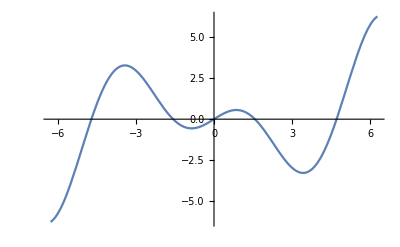

```mathematica
$TextStyle={FontSize->14}
p1=Plot[Cos[x]*x,{x,-2π,2π}]
```

Отметим, что результатом команды Plot является специальный графический объект Mathematica, для отображения которого на экране используется термин -Graphics-. Именно этот объект в данном случае будет значением переменной p1. Сам же рисунок, вообще говоря, является лишь "побочным эффектом" выполнения команды и его наличие или отсутствие на экране регулируется специальной опцией.

Команда Plot позволяет изобразить на одном рисунке графики сразу нескольких функций для одной и той же области изменения их общего аргумента:

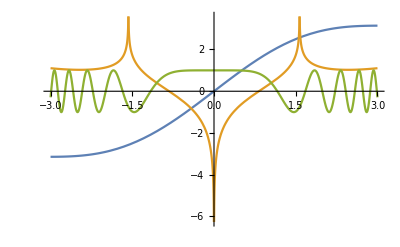

```mathematica
p2=Plot[{x+Sin[x],Log[Abs[x/(√Cos[x])]],Cos[x^3]},
                                                                                        {x,-3,3}]
```

Команда Plot3D для построения трехмерных графиков функций двух переменных имеет аналогичную форму записи, с той лишь разницей, что в ней необходимо указывать области изменения для двух переменных:

```mathematica
$TextStyle={FontSize->14}
p3=Plot3D[Sin[2x]*Sin[3x+y],
                                             {x,-1,1},{y,-3,3}]
```

{FontSize→14}

-Graphics3D-

Для построения двумерных и трехмерных графиков функций, заданных параметрически, используются команды ParametricPlot и ParametricPlot3D соответственно.

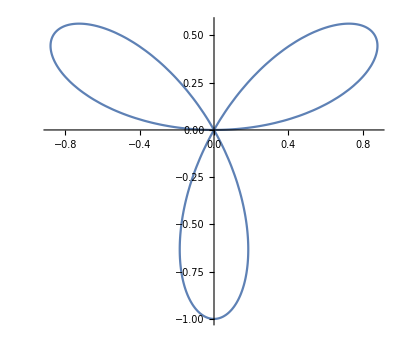

```mathematica
p4=ParametricPlot[{Cos[t] Sin[3 t], Sin[t] Sin[3 t]},{t,0,Pi}]
```

Команда ParametricPlot3D может использоваться для построения как кривых (один параметр), так и поверхностей (два параметра).

```mathematica
p5=ParametricPlot3D[{Sin[t/8]Cos[t],Sin[t/8]Sin[t],t/8},{t,0,8Pi},PlotPoints->1000]
```

-Graphics3D-

```mathematica
$TextStyle={FontSize->14}
p6=ParametricPlot3D[{ Cos[p]+Sin[t] , Sin[p] + Cos[t],t},{p,0,2Pi},{t,-Pi,Pi}]
```

{FontSize→14}

-Graphics3D-

Нечто среднее между двумерным и трехмерным графиком можно получить с помощью функции ContourPlot. Эта функция служит для построения контурного изображения трехмерной поверхности.

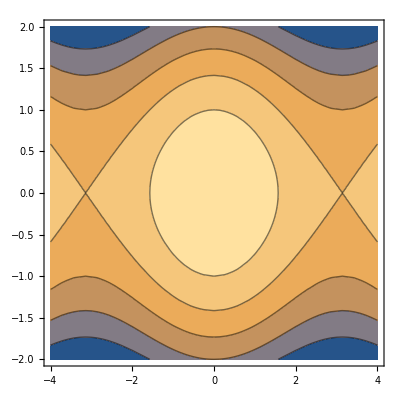

```mathematica
p7 = ContourPlot[Cos[x] - y^2, 
                    {x, -4, 4}, {y, -2, 2}]
```

Визуализация содержимого числовых списков производится командами ListPlot и ListPlot3D. Единственным аргументом команды ListPlot может быть числовой одномерный список. В построенном графике по горизонтальной оси будут откладываться порядковые номера элементов списка, а по вертикальной — значения этих элементов.

{FontSize→14}

{0,Cos[1] Sin[1],√2 Cos[2] Sin[2],√3 Cos[3] Sin[3],2 Cos[4] Sin[4],√5 Cos[5] Sin[5],√6 Cos[6] Sin[6],√7 Cos[7] Sin[7],2 √2 Cos[8] Sin[8],3 Cos[9] Sin[9],√10 Cos[10] Sin[10],√11 Cos[11] Sin[11],2 √3 Cos[12] Sin[12],√13 Cos[13] Sin[13],√14 Cos[14] Sin[14],√15 Cos[15] Sin[15],4 Cos[16] Sin[16],√17 Cos[17] Sin[17],3 √2 Cos[18] Sin[18],√19 Cos[19] Sin[19],2 √5 Cos[20] Sin[20],√21 Cos[21] Sin[21],√22 Cos[22] Sin[22],√23 Cos[23] Sin[23],2 √6 Cos[24] Sin[24],5 Cos[25] Sin[25],√26 Cos[26] Sin[26],3 √3 Cos[27] Sin[27],2 √7 Cos[28] Sin[28],√29 Cos[29] Sin[29],√30 Cos[30] Sin[30],√31 Cos[31] Sin[31],4 √2 Cos[32] Sin[32],√33 Cos[33] Sin[33],√34 Cos[34] Sin[34],√35 Cos[35] Sin[35],6 Cos[36] Sin[36],√37 Cos[37] Sin[37],√38 Cos[38] Sin[38],√39 Cos[39] Sin[39],2 √10 Cos[40] Sin[40],√41 Cos[41] Sin[41],√42 Cos[42] Sin[42],√43 Cos[43] Sin[43],2 √11 Cos[44] Sin[44],3 √5 Cos[45] Sin[45],√46 Cos[46] Sin[46],√47 Cos[47] Sin[47],4 √3 Cos[48] Sin[48],7 Cos[49] Sin[49],5 √2 Cos[50] Sin[50],√51 Cos[51] Sin[51],2 √13 Cos[52] Sin[52],√53 Cos[53] Sin[53],3 √6 Cos[54] Sin[54],√55 Cos[55] Sin[55],2 √14 Cos[56] Sin[56],√57 Cos[57] Sin[57],√58 Cos[58] Sin[58],√59 Cos[59] Sin[59],2 √15 Cos[60] Sin[60],√61 Cos[61] Sin[61],√62 Cos[62] Sin[62],3 √7 Cos[63] Sin[63],8 Cos[64] Sin[64],√65 Cos[65] Sin[65],√66 Cos[66] Sin[66],√67 Cos[67] Sin[67],2 √17 Cos[68] Sin[68],√69 Cos[69] Sin[69],√70 Cos[70] Sin[70],√71 Cos[71] Sin[71],6 √2 Cos[72] Sin[72],√73 Cos[73] Sin[73],√74 Cos[74] Sin[74],5 √3 Cos[75] Sin[75],2 √19 Cos[76] Sin[76],√77 Cos[77] Sin[77],√78 Cos[78] Sin[78],√79 Cos[79] Sin[79],4 √5 Cos[80] Sin[80],9 Cos[81] Sin[81],√82 Cos[82] Sin[82],√83 Cos[83] Sin[83],2 √21 Cos[84] Sin[84],√85 Cos[85] Sin[85],√86 Cos[86] Sin[86],√87 Cos[87] Sin[87],2 √22 Cos[88] Sin[88],√89 Cos[89] Sin[89],3 √10 Cos[90] Sin[90],√91 Cos[91] Sin[91],2 √23 Cos[92] Sin[92],√93 Cos[93] Sin[93],√94 Cos[94] Sin[94],√95 Cos[95] Sin[95],4 √6 Cos[96] Sin[96],√97 Cos[97] Sin[97],7 √2 Cos[98] Sin[98],3 √11 Cos[99] Sin[99],10 Cos[100] Sin[100],√101 Cos[101] Sin[101],√102 Cos[102] Sin[102],√103 Cos[103] Sin[103],2 √26 Cos[104] Sin[104],√105 Cos[105] Sin[105],√106 Cos[106] Sin[106],√107 Cos[107] Sin[107],6 √3 Cos[108] Sin[108],√109 Cos[109] Sin[109],√110 Cos[110] Sin[110],√111 Cos[111] Sin[111],4 √7 Cos[112] Sin[112],√113 Cos[113] Sin[113],√114 Cos[114] Sin[114],√115 Cos[115] Sin[115],2 √29 Cos[116] Sin[116],3 √13 Cos[117] Sin[117],√118 Cos[118] Sin[118],√119 Cos[119] Sin[119],2 √30 Cos[120] Sin[120],11 Cos[121] Sin[121],√122 Cos[122] Sin[122],√123 Cos[123] Sin[123],2 √31 Cos[124] Sin[124],5 √5 Cos[125] Sin[125],3 √14 Cos[126] Sin[126],√127 Cos[127] Sin[127],8 √2 Cos[128] Sin[128],√129 Cos[129] Sin[129],√130 Cos[130] Sin[130],√131 Cos[131] Sin[131],2 √33 Cos[132] Sin[132],√133 Cos[133] Sin[133],√134 Cos[134] Sin[134],3 √15 Cos[135] Sin[135],2 √34 Cos[136] Sin[136],√137 Cos[137] Sin[137],√138 Cos[138] Sin[138],√139 Cos[139] Sin[139],2 √35 Cos[140] Sin[140],√141 Cos[141] Sin[141],√142 Cos[142] Sin[142],√143 Cos[143] Sin[143],12 Cos[144] Sin[144],√145 Cos[145] Sin[145],√146 Cos[146] Sin[146],7 √3 Cos[147] Sin[147],2 √37 Cos[148] Sin[148],√149 Cos[149] Sin[149],5 √6 Cos[150] Sin[150],√151 Cos[151] Sin[151],2 √38 Cos[152] Sin[152],3 √17 Cos[153] Sin[153],√154 Cos[154] Sin[154],√155 Cos[155] Sin[155],2 √39 Cos[156] Sin[156],√157 Cos[157] Sin[157],√158 Cos[158] Sin[158],√159 Cos[159] Sin[159],4 √10 Cos[160] Sin[160],√161 Cos[161] Sin[161],9 √2 Cos[162] Sin[162],√163 Cos[163] Sin[163],2 √41 Cos[164] Sin[164],√165 Cos[165] Sin[165],√166 Cos[166] Sin[166],√167 Cos[167] Sin[167],2 √42 Cos[168] Sin[168],13 Cos[169] Sin[169],√170 Cos[170] Sin[170],3 √19 Cos[171] Sin[171],2 √43 Cos[172] Sin[172],√173 Cos[173] Sin[173],√174 Cos[174] Sin[174],5 √7 Cos[175] Sin[175],4 √11 Cos[176] Sin[176],√177 Cos[177] Sin[177],√178 Cos[178] Sin[178],√179 Cos[179] Sin[179],6 √5 Cos[180] Sin[180],√181 Cos[181] Sin[181],√182 Cos[182] Sin[182],√183 Cos[183] Sin[183],2 √46 Cos[184] Sin[184],√185 Cos[185] Sin[185],√186 Cos[186] Sin[186],√187 Cos[187] Sin[187],2 √47 Cos[188] Sin[188],3 √21 Cos[189] Sin[189],√190 Cos[190] Sin[190],√191 Cos[191] Sin[191],8 √3 Cos[192] Sin[192],√193 Cos[193] Sin[193],√194 Cos[194] Sin[194],√195 Cos[195] Sin[195],14 Cos[196] Sin[196],√197 Cos[197] Sin[197],3 √22 Cos[198] Sin[198],√199 Cos[199] Sin[199],10 √2 Cos[200] Sin[200],√201 Cos[201] Sin[201],√202 Cos[202] Sin[202],√203 Cos[203] Sin[203],2 √51 Cos[204] Sin[204],√205 Cos[205] Sin[205],√206 Cos[206] Sin[206],3 √23 Cos[207] Sin[207],4 √13 Cos[208] Sin[208],√209 Cos[209] Sin[209],√210 Cos[210] Sin[210],√211 Cos[211] Sin[211],2 √53 Cos[212] Sin[212],√213 Cos[213] Sin[213],√214 Cos[214] Sin[214],√215 Cos[215] Sin[215],6 √6 Cos[216] Sin[216],√217 Cos[217] Sin[217],√218 Cos[218] Sin[218],√219 Cos[219] Sin[219],2 √55 Cos[220] Sin[220],√221 Cos[221] Sin[221],√222 Cos[222] Sin[222],√223 Cos[223] Sin[223],4 √14 Cos[224] Sin[224],15 Cos[225] Sin[225],√226 Cos[226] Sin[226],√227 Cos[227] Sin[227],2 √57 Cos[228] Sin[228],√229 Cos[229] Sin[229],√230 Cos[230] Sin[230],√231 Cos[231] Sin[231],2 √58 Cos[232] Sin[232],√233 Cos[233] Sin[233],3 √26 Cos[234] Sin[234],√235 Cos[235] Sin[235],2 √59 Cos[236] Sin[236],√237 Cos[237] Sin[237],√238 Cos[238] Sin[238],√239 Cos[239] Sin[239],4 √15 Cos[240] Sin[240],√241 Cos[241] Sin[241],11 √2 Cos[242] Sin[242],9 √3 Cos[243] Sin[243],2 √61 Cos[244] Sin[244],7 √5 Cos[245] Sin[245],√246 Cos[246] Sin[246],√247 Cos[247] Sin[247],2 √62 Cos[248] Sin[248],√249 Cos[249] Sin[249],5 √10 Cos[250] Sin[250],√251 Cos[251] Sin[251],6 √7 Cos[252] Sin[252],√253 Cos[253] Sin[253],√254 Cos[254] Sin[254],√255 Cos[255] Sin[255],16 Cos[256] Sin[256],√257 Cos[257] Sin[257],√258 Cos[258] Sin[258],√259 Cos[259] Sin[259],2 √65 Cos[260] Sin[260],3 √29 Cos[261] Sin[261],√262 Cos[262] Sin[262],√263 Cos[263] Sin[263],2 √66 Cos[264] Sin[264],√265 Cos[265] Sin[265],√266 Cos[266] Sin[266],√267 Cos[267] Sin[267],2 √67 Cos[268] Sin[268],√269 Cos[269] Sin[269],3 √30 Cos[270] Sin[270],√271 Cos[271] Sin[271],4 √17 Cos[272] Sin[272],√273 Cos[273] Sin[273],√274 Cos[274] Sin[274],5 √11 Cos[275] Sin[275],2 √69 Cos[276] Sin[276],√277 Cos[277] Sin[277],√278 Cos[278] Sin[278],3 √31 Cos[279] Sin[279],2 √70 Cos[280] Sin[280],√281 Cos[281] Sin[281],√282 Cos[282] Sin[282],√283 Cos[283] Sin[283],2 √71 Cos[284] Sin[284],√285 Cos[285] Sin[285],√286 Cos[286] Sin[286],√287 Cos[287] Sin[287],12 √2 Cos[288] Sin[288],17 Cos[289] Sin[289],√290 Cos[290] Sin[290],√291 Cos[291] Sin[291],2 √73 Cos[292] Sin[292],√293 Cos[293] Sin[293],7 √6 Cos[294] Sin[294],√295 Cos[295] Sin[295],2 √74 Cos[296] Sin[296],3 √33 Cos[297] Sin[297],√298 Cos[298] Sin[298],√299 Cos[299] Sin[299],10 √3 Cos[300] Sin[300],√301 Cos[301] Sin[301],√302 Cos[302] Sin[302],√303 Cos[303] Sin[303],4 √19 Cos[304] Sin[304],√305 Cos[305] Sin[305],3 √34 Cos[306] Sin[306],√307 Cos[307] Sin[307],2 √77 Cos[308] Sin[308],√309 Cos[309] Sin[309],√310 Cos[310] Sin[310],√311 Cos[311] Sin[311],2 √78 Cos[312] Sin[312],√313 Cos[313] Sin[313],√314 Cos[314] Sin[314],3 √35 Cos[315] Sin[315],2 √79 Cos[316] Sin[316],√317 Cos[317] Sin[317],√318 Cos[318] Sin[318],√319 Cos[319] Sin[319],8 √5 Cos[320] Sin[320],√321 Cos[321] Sin[321],√322 Cos[322] Sin[322],√323 Cos[323] Sin[323],18 Cos[324] Sin[324],5 √13 Cos[325] Sin[325],√326 Cos[326] Sin[326],√327 Cos[327] Sin[327],2 √82 Cos[328] Sin[328],√329 Cos[329] Sin[329],√330 Cos[330] Sin[330],√331 Cos[331] Sin[331],2 √83 Cos[332] Sin[332],3 √37 Cos[333] Sin[333],√334 Cos[334] Sin[334],√335 Cos[335] Sin[335],4 √21 Cos[336] Sin[336],√337 Cos[337] Sin[337],13 √2 Cos[338] Sin[338],√339 Cos[339] Sin[339],2 √85 Cos[340] Sin[340],√341 Cos[341] Sin[341],3 √38 Cos[342] Sin[342],7 √7 Cos[343] Sin[343],2 √86 Cos[344] Sin[344],√345 Cos[345] Sin[345],√346 Cos[346] Sin[346],√347 Cos[347] Sin[347],2 √87 Cos[348] Sin[348],√349 Cos[349] Sin[349],5 √14 Cos[350] Sin[350],3 √39 Cos[351] Sin[351],4 √22 Cos[352] Sin[352],√353 Cos[353] Sin[353],√354 Cos[354] Sin[354],√355 Cos[355] Sin[355],2 √89 Cos[356] Sin[356],√357 Cos[357] Sin[357],√358 Cos[358] Sin[358],√359 Cos[359] Sin[359],6 √10 Cos[360] Sin[360],19 Cos[361] Sin[361],√362 Cos[362] Sin[362],11 √3 Cos[363] Sin[363],2 √91 Cos[364] Sin[364],√365 Cos[365] Sin[365],√366 Cos[366] Sin[366],√367 Cos[367] Sin[367],4 √23 Cos[368] Sin[368],3 √41 Cos[369] Sin[369],√370 Cos[370] Sin[370],√371 Cos[371] Sin[371],2 √93 Cos[372] Sin[372],√373 Cos[373] Sin[373],√374 Cos[374] Sin[374],5 √15 Cos[375] Sin[375],2 √94 Cos[376] Sin[376],√377 Cos[377] Sin[377],3 √42 Cos[378] Sin[378],√379 Cos[379] Sin[379],2 √95 Cos[380] Sin[380],√381 Cos[381] Sin[381],√382 Cos[382] Sin[382],√383 Cos[383] Sin[383],8 √6 Cos[384] Sin[384],√385 Cos[385] Sin[385],√386 Cos[386] Sin[386],3 √43 Cos[387] Sin[387],2 √97 Cos[388] Sin[388],√389 Cos[389] Sin[389],√390 Cos[390] Sin[390],√391 Cos[391] Sin[391],14 √2 Cos[392] Sin[392],√393 Cos[393] Sin[393],√394 Cos[394] Sin[394],√395 Cos[395] Sin[395],6 √11 Cos[396] Sin[396],√397 Cos[397] Sin[397],√398 Cos[398] Sin[398],√399 Cos[399] Sin[399],20 Cos[400] Sin[400],√401 Cos[401] Sin[401],√402 Cos[402] Sin[402],√403 Cos[403] Sin[403],2 √101 Cos[404] Sin[404],9 √5 Cos[405] Sin[405],√406 Cos[406] Sin[406],√407 Cos[407] Sin[407],2 √102 Cos[408] Sin[408],√409 Cos[409] Sin[409],√410 Cos[410] Sin[410],√411 Cos[411] Sin[411],2 √103 Cos[412] Sin[412],√413 Cos[413] Sin[413],3 √46 Cos[414] Sin[414],√415 Cos[415] Sin[415],4 √26 Cos[416] Sin[416],√417 Cos[417] Sin[417],√418 Cos[418] Sin[418],√419 Cos[419] Sin[419],2 √105 Cos[420] Sin[420],√421 Cos[421] Sin[421],√422 Cos[422] Sin[422],3 √47 Cos[423] Sin[423],2 √106 Cos[424] Sin[424],5 √17 Cos[425] Sin[425],√426 Cos[426] Sin[426],√427 Cos[427] Sin[427],2 √107 Cos[428] Sin[428],√429 Cos[429] Sin[429],√430 Cos[430] Sin[430],√431 Cos[431] Sin[431],12 √3 Cos[432] Sin[432],√433 Cos[433] Sin[433],√434 Cos[434] Sin[434],√435 Cos[435] Sin[435],2 √109 Cos[436] Sin[436],√437 Cos[437] Sin[437],√438 Cos[438] Sin[438],√439 Cos[439] Sin[439],2 √110 Cos[440] Sin[440],21 Cos[441] Sin[441],√442 Cos[442] Sin[442],√443 Cos[443] Sin[443],2 √111 Cos[444] Sin[444],√445 Cos[445] Sin[445],√446 Cos[446] Sin[446],√447 Cos[447] Sin[447],8 √7 Cos[448] Sin[448],√449 Cos[449] Sin[449],15 √2 Cos[450] Sin[450],√451 Cos[451] Sin[451],2 √113 Cos[452] Sin[452],√453 Cos[453] Sin[453],√454 Cos[454] Sin[454],√455 Cos[455] Sin[455],2 √114 Cos[456] Sin[456],√457 Cos[457] Sin[457],√458 Cos[458] Sin[458],3 √51 Cos[459] Sin[459],2 √115 Cos[460] Sin[460],√461 Cos[461] Sin[461],√462 Cos[462] Sin[462],√463 Cos[463] Sin[463],4 √29 Cos[464] Sin[464],√465 Cos[465] Sin[465],√466 Cos[466] Sin[466],√467 Cos[467] Sin[467],6 √13 Cos[468] Sin[468],√469 Cos[469] Sin[469],√470 Cos[470] Sin[470],√471 Cos[471] Sin[471],2 √118 Cos[472] Sin[472],√473 Cos[473] Sin[473],√474 Cos[474] Sin[474],5 √19 Cos[475] Sin[475],2 √119 Cos[476] Sin[476],3 √53 Cos[477] Sin[477],√478 Cos[478] Sin[478],√479 Cos[479] Sin[479],4 √30 Cos[480] Sin[480],√481 Cos[481] Sin[481],√482 Cos[482] Sin[482],√483 Cos[483] Sin[483],22 Cos[484] Sin[484],√485 Cos[485] Sin[485],9 √6 Cos[486] Sin[486],√487 Cos[487] Sin[487],2 √122 Cos[488] Sin[488],√489 Cos[489] Sin[489],7 √10 Cos[490] Sin[490],√491 Cos[491] Sin[491],2 √123 Cos[492] Sin[492],√493 Cos[493] Sin[493],√494 Cos[494] Sin[494],3 √55 Cos[495] Sin[495],4 √31 Cos[496] Sin[496],√497 Cos[497] Sin[497],√498 Cos[498] Sin[498],√499 Cos[499] Sin[499],10 √5 Cos[500] Sin[500],√501 Cos[501] Sin[501],√502 Cos[502] Sin[502],√503 Cos[503] Sin[503],6 √14 Cos[504] Sin[504],√505 Cos[505] Sin[505],√506 Cos[506] Sin[506],13 √3 Cos[507] Sin[507],2 √127 Cos[508] Sin[508],√509 Cos[509] Sin[509],√510 Cos[510] Sin[510],√511 Cos[511] Sin[511],16 √2 Cos[512] Sin[512],3 √57 Cos[513] Sin[513],√514 Cos[514] Sin[514],√515 Cos[515] Sin[515],2 √129 Cos[516] Sin[516],√517 Cos[517] Sin[517],√518 Cos[518] Sin[518],√519 Cos[519] Sin[519],2 √130 Cos[520] Sin[520],√521 Cos[521] Sin[521],3 √58 Cos[522] Sin[522],√523 Cos[523] Sin[523],2 √131 Cos[524] Sin[524],5 √21 Cos[525] Sin[525],√526 Cos[526] Sin[526],√527 Cos[527] Sin[527],4 √33 Cos[528] Sin[528],23 Cos[529] Sin[529],√530 Cos[530] Sin[530],3 √59 Cos[531] Sin[531],2 √133 Cos[532] Sin[532],√533 Cos[533] Sin[533],√534 Cos[534] Sin[534],√535 Cos[535] Sin[535],2 √134 Cos[536] Sin[536],√537 Cos[537] Sin[537],√538 Cos[538] Sin[538],7 √11 Cos[539] Sin[539],6 √15 Cos[540] Sin[540],√541 Cos[541] Sin[541],√542 Cos[542] Sin[542],√543 Cos[543] Sin[543],4 √34 Cos[544] Sin[544],√545 Cos[545] Sin[545],√546 Cos[546] Sin[546],√547 Cos[547] Sin[547],2 √137 Cos[548] Sin[548],3 √61 Cos[549] Sin[549],5 √22 Cos[550] Sin[550],√551 Cos[551] Sin[551],2 √138 Cos[552] Sin[552],√553 Cos[553] Sin[553],√554 Cos[554] Sin[554],√555 Cos[555] Sin[555],2 √139 Cos[556] Sin[556],√557 Cos[557] Sin[557],3 √62 Cos[558] Sin[558],√559 Cos[559] Sin[559],4 √35 Cos[560] Sin[560],√561 Cos[561] Sin[561],√562 Cos[562] Sin[562],√563 Cos[563] Sin[563],2 √141 Cos[564] Sin[564],√565 Cos[565] Sin[565],√566 Cos[566] Sin[566],9 √7 Cos[567] Sin[567],2 √142 Cos[568] Sin[568],√569 Cos[569] Sin[569],√570 Cos[570] Sin[570],√571 Cos[571] Sin[571],2 √143 Cos[572] Sin[572],√573 Cos[573] Sin[573],√574 Cos[574] Sin[574],5 √23 Cos[575] Sin[575],24 Cos[576] Sin[576],√577 Cos[577] Sin[577],17 √2 Cos[578] Sin[578],√579 Cos[579] Sin[579],2 √145 Cos[580] Sin[580],√581 Cos[581] Sin[581],√582 Cos[582] Sin[582],√583 Cos[583] Sin[583],2 √146 Cos[584] Sin[584],3 √65 Cos[585] Sin[585],√586 Cos[586] Sin[586],√587 Cos[587] Sin[587],14 √3 Cos[588] Sin[588],√589 Cos[589] Sin[589],√590 Cos[590] Sin[590],√591 Cos[591] Sin[591],4 √37 Cos[592] Sin[592],√593 Cos[593] Sin[593],3 √66 Cos[594] Sin[594],√595 Cos[595] Sin[595],2 √149 Cos[596] Sin[596],√597 Cos[597] Sin[597],√598 Cos[598] Sin[598],√599 Cos[599] Sin[599],10 √6 Cos[600] Sin[600],√601 Cos[601] Sin[601],√602 Cos[602] Sin[602],3 √67 Cos[603] Sin[603],2 √151 Cos[604] Sin[604],11 √5 Cos[605] Sin[605],√606 Cos[606] Sin[606],√607 Cos[607] Sin[607],4 √38 Cos[608] Sin[608],√609 Cos[609] Sin[609],√610 Cos[610] Sin[610],√611 Cos[611] Sin[611],6 √17 Cos[612] Sin[612],√613 Cos[613] Sin[613],√614 Cos[614] Sin[614],√615 Cos[615] Sin[615],2 √154 Cos[616] Sin[616],√617 Cos[617] Sin[617],√618 Cos[618] Sin[618],√619 Cos[619] Sin[619],2 √155 Cos[620] Sin[620],3 √69 Cos[621] Sin[621],√622 Cos[622] Sin[622],√623 Cos[623] Sin[623],4 √39 Cos[624] Sin[624],25 Cos[625] Sin[625],√626 Cos[626] Sin[626],√627 Cos[627] Sin[627],2 √157 Cos[628] Sin[628],√629 Cos[629] Sin[629],3 √70 Cos[630] Sin[630],√631 Cos[631] Sin[631],2 √158 Cos[632] Sin[632],√633 Cos[633] Sin[633],√634 Cos[634] Sin[634],√635 Cos[635] Sin[635],2 √159 Cos[636] Sin[636],7 √13 Cos[637] Sin[637],√638 Cos[638] Sin[638],3 √71 Cos[639] Sin[639],8 √10 Cos[640] Sin[640],√641 Cos[641] Sin[641],√642 Cos[642] Sin[642],√643 Cos[643] Sin[643],2 √161 Cos[644] Sin[644],√645 Cos[645] Sin[645],√646 Cos[646] Sin[646],√647 Cos[647] Sin[647],18 √2 Cos[648] Sin[648],√649 Cos[649] Sin[649],5 √26 Cos[650] Sin[650],√651 Cos[651] Sin[651],2 √163 Cos[652] Sin[652],√653 Cos[653] Sin[653],√654 Cos[654] Sin[654],√655 Cos[655] Sin[655],4 √41 Cos[656] Sin[656],3 √73 Cos[657] Sin[657],√658 Cos[658] Sin[658],√659 Cos[659] Sin[659],2 √165 Cos[660] Sin[660],√661 Cos[661] Sin[661],√662 Cos[662] Sin[662],√663 Cos[663] Sin[663],2 √166 Cos[664] Sin[664],√665 Cos[665] Sin[665],3 √74 Cos[666] Sin[666],√667 Cos[667] Sin[667],2 √167 Cos[668] Sin[668],√669 Cos[669] Sin[669],√670 Cos[670] Sin[670],√671 Cos[671] Sin[671],4 √42 Cos[672] Sin[672],√673 Cos[673] Sin[673],√674 Cos[674] Sin[674],15 √3 Cos[675] Sin[675],26 Cos[676] Sin[676],√677 Cos[677] Sin[677],√678 Cos[678] Sin[678],√679 Cos[679] Sin[679],2 √170 Cos[680] Sin[680],√681 Cos[681] Sin[681],√682 Cos[682] Sin[682],√683 Cos[683] Sin[683],6 √19 Cos[684] Sin[684],√685 Cos[685] Sin[685],7 √14 Cos[686] Sin[686],√687 Cos[687] Sin[687],4 √43 Cos[688] Sin[688],√689 Cos[689] Sin[689],√690 Cos[690] Sin[690],√691 Cos[691] Sin[691],2 √173 Cos[692] Sin[692],3 √77 Cos[693] Sin[693],√694 Cos[694] Sin[694],√695 Cos[695] Sin[695],2 √174 Cos[696] Sin[696],√697 Cos[697] Sin[697],√698 Cos[698] Sin[698],√699 Cos[699] Sin[699],10 √7 Cos[700] Sin[700],√701 Cos[701] Sin[701],3 √78 Cos[702] Sin[702],√703 Cos[703] Sin[703],8 √11 Cos[704] Sin[704],√705 Cos[705] Sin[705],√706 Cos[706] Sin[706],√707 Cos[707] Sin[707],2 √177 Cos[708] Sin[708],√709 Cos[709] Sin[709],√710 Cos[710] Sin[710],3 √79 Cos[711] Sin[711],2 √178 Cos[712] Sin[712],√713 Cos[713] Sin[713],√714 Cos[714] Sin[714],√715 Cos[715] Sin[715],2 √179 Cos[716] Sin[716],√717 Cos[717] Sin[717],√718 Cos[718] Sin[718],√719 Cos[719] Sin[719],12 √5 Cos[720] Sin[720],√721 Cos[721] Sin[721],19 √2 Cos[722] Sin[722],√723 Cos[723] Sin[723],2 √181 Cos[724] Sin[724],5 √29 Cos[725] Sin[725],11 √6 Cos[726] Sin[726],√727 Cos[727] Sin[727],2 √182 Cos[728] Sin[728],27 Cos[729] Sin[729],√730 Cos[730] Sin[730],√731 Cos[731] Sin[731],2 √183 Cos[732] Sin[732],√733 Cos[733] Sin[733],√734 Cos[734] Sin[734],7 √15 Cos[735] Sin[735],4 √46 Cos[736] Sin[736],√737 Cos[737] Sin[737],3 √82 Cos[738] Sin[738],√739 Cos[739] Sin[739],2 √185 Cos[740] Sin[740],√741 Cos[741] Sin[741],√742 Cos[742] Sin[742],√743 Cos[743] Sin[743],2 √186 Cos[744] Sin[744],√745 Cos[745] Sin[745],√746 Cos[746] Sin[746],3 √83 Cos[747] Sin[747],2 √187 Cos[748] Sin[748],√749 Cos[749] Sin[749],5 √30 Cos[750] Sin[750],√751 Cos[751] Sin[751],4 √47 Cos[752] Sin[752],√753 Cos[753] Sin[753],√754 Cos[754] Sin[754],√755 Cos[755] Sin[755],6 √21 Cos[756] Sin[756],√757 Cos[757] Sin[757],√758 Cos[758] Sin[758],√759 Cos[759] Sin[759],2 √190 Cos[760] Sin[760],√761 Cos[761] Sin[761],√762 Cos[762] Sin[762],√763 Cos[763] Sin[763],2 √191 Cos[764] Sin[764],3 √85 Cos[765] Sin[765],√766 Cos[766] Sin[766],√767 Cos[767] Sin[767],16 √3 Cos[768] Sin[768],√769 Cos[769] Sin[769],√770 Cos[770] Sin[770],√771 Cos[771] Sin[771],2 √193 Cos[772] Sin[772],√773 Cos[773] Sin[773],3 √86 Cos[774] Sin[774],5 √31 Cos[775] Sin[775],2 √194 Cos[776] Sin[776],√777 Cos[777] Sin[777],√778 Cos[778] Sin[778],√779 Cos[779] Sin[779],2 √195 Cos[780] Sin[780],√781 Cos[781] Sin[781],√782 Cos[782] Sin[782],3 √87 Cos[783] Sin[783],28 Cos[784] Sin[784],√785 Cos[785] Sin[785],√786 Cos[786] Sin[786],√787 Cos[787] Sin[787],2 √197 Cos[788] Sin[788],√789 Cos[789] Sin[789],√790 Cos[790] Sin[790],√791 Cos[791] Sin[791],6 √22 Cos[792] Sin[792],√793 Cos[793] Sin[793],√794 Cos[794] Sin[794],√795 Cos[795] Sin[795],2 √199 Cos[796] Sin[796],√797 Cos[797] Sin[797],√798 Cos[798] Sin[798],√799 Cos[799] Sin[799],20 √2 Cos[800] Sin[800],3 √89 Cos[801] Sin[801],√802 Cos[802] Sin[802],√803 Cos[803] Sin[803],2 √201 Cos[804] Sin[804],√805 Cos[805] Sin[805],√806 Cos[806] Sin[806],√807 Cos[807] Sin[807],2 √202 Cos[808] Sin[808],√809 Cos[809] Sin[809],9 √10 Cos[810] Sin[810],√811 Cos[811] Sin[811],2 √203 Cos[812] Sin[812],√813 Cos[813] Sin[813],√814 Cos[814] Sin[814],√815 Cos[815] Sin[815],4 √51 Cos[816] Sin[816],√817 Cos[817] Sin[817],√818 Cos[818] Sin[818],3 √91 Cos[819] Sin[819],2 √205 Cos[820] Sin[820],√821 Cos[821] Sin[821],√822 Cos[822] Sin[822],√823 Cos[823] Sin[823],2 √206 Cos[824] Sin[824],5 √33 Cos[825] Sin[825],√826 Cos[826] Sin[826],√827 Cos[827] Sin[827],6 √23 Cos[828] Sin[828],√829 Cos[829] Sin[829],√830 Cos[830] Sin[830],√831 Cos[831] Sin[831],8 √13 Cos[832] Sin[832],7 √17 Cos[833] Sin[833],√834 Cos[834] Sin[834],√835 Cos[835] Sin[835],2 √209 Cos[836] Sin[836],3 √93 Cos[837] Sin[837],√838 Cos[838] Sin[838],√839 Cos[839] Sin[839],2 √210 Cos[840] Sin[840],29 Cos[841] Sin[841],√842 Cos[842] Sin[842],√843 Cos[843] Sin[843],2 √211 Cos[844] Sin[844],13 √5 Cos[845] Sin[845],3 √94 Cos[846] Sin[846],11 √7 Cos[847] Sin[847],4 √53 Cos[848] Sin[848],√849 Cos[849] Sin[849],5 √34 Cos[850] Sin[850],√851 Cos[851] Sin[851],2 √213 Cos[852] Sin[852],√853 Cos[853] Sin[853],√854 Cos[854] Sin[854],3 √95 Cos[855] Sin[855],2 √214 Cos[856] Sin[856],√857 Cos[857] Sin[857],√858 Cos[858] Sin[858],√859 Cos[859] Sin[859],2 √215 Cos[860] Sin[860],√861 Cos[861] Sin[861],√862 Cos[862] Sin[862],√863 Cos[863] Sin[863],12 √6 Cos[864] Sin[864],√865 Cos[865] Sin[865],√866 Cos[866] Sin[866],17 √3 Cos[867] Sin[867],2 √217 Cos[868] Sin[868],√869 Cos[869] Sin[869],√870 Cos[870] Sin[870],√871 Cos[871] Sin[871],2 √218 Cos[872] Sin[872],3 √97 Cos[873] Sin[873],√874 Cos[874] Sin[874],5 √35 Cos[875] Sin[875],2 √219 Cos[876] Sin[876],√877 Cos[877] Sin[877],√878 Cos[878] Sin[878],√879 Cos[879] Sin[879],4 √55 Cos[880] Sin[880],√881 Cos[881] Sin[881],21 √2 Cos[882] Sin[882],√883 Cos[883] Sin[883],2 √221 Cos[884] Sin[884],√885 Cos[885] Sin[885],√886 Cos[886] Sin[886],√887 Cos[887] Sin[887],2 √222 Cos[888] Sin[888],√889 Cos[889] Sin[889],√890 Cos[890] Sin[890],9 √11 Cos[891] Sin[891],2 √223 Cos[892] Sin[892],√893 Cos[893] Sin[893],√894 Cos[894] Sin[894],√895 Cos[895] Sin[895],8 √14 Cos[896] Sin[896],√897 Cos[897] Sin[897],√898 Cos[898] Sin[898],√899 Cos[899] Sin[899],30 Cos[900] Sin[900],√901 Cos[901] Sin[901],√902 Cos[902] Sin[902],√903 Cos[903] Sin[903],2 √226 Cos[904] Sin[904],√905 Cos[905] Sin[905],√906 Cos[906] Sin[906],√907 Cos[907] Sin[907],2 √227 Cos[908] Sin[908],3 √101 Cos[909] Sin[909],√910 Cos[910] Sin[910],√911 Cos[911] Sin[911],4 √57 Cos[912] Sin[912],√913 Cos[913] Sin[913],√914 Cos[914] Sin[914],√915 Cos[915] Sin[915],2 √229 Cos[916] Sin[916],√917 Cos[917] Sin[917],3 √102 Cos[918] Sin[918],√919 Cos[919] Sin[919],2 √230 Cos[920] Sin[920],√921 Cos[921] Sin[921],√922 Cos[922] Sin[922],√923 Cos[923] Sin[923],2 √231 Cos[924] Sin[924],5 √37 Cos[925] Sin[925],√926 Cos[926] Sin[926],3 √103 Cos[927] Sin[927],4 √58 Cos[928] Sin[928],√929 Cos[929] Sin[929],√930 Cos[930] Sin[930],7 √19 Cos[931] Sin[931],2 √233 Cos[932] Sin[932],√933 Cos[933] Sin[933],√934 Cos[934] Sin[934],√935 Cos[935] Sin[935],6 √26 Cos[936] Sin[936],√937 Cos[937] Sin[937],√938 Cos[938] Sin[938],√939 Cos[939] Sin[939],2 √235 Cos[940] Sin[940],√941 Cos[941] Sin[941],√942 Cos[942] Sin[942],√943 Cos[943] Sin[943],4 √59 Cos[944] Sin[944],3 √105 Cos[945] Sin[945],√946 Cos[946] Sin[946],√947 Cos[947] Sin[947],2 √237 Cos[948] Sin[948],√949 Cos[949] Sin[949],5 √38 Cos[950] Sin[950],√951 Cos[951] Sin[951],2 √238 Cos[952] Sin[952],√953 Cos[953] Sin[953],3 √106 Cos[954] Sin[954],√955 Cos[955] Sin[955],2 √239 Cos[956] Sin[956],√957 Cos[957] Sin[957],√958 Cos[958] Sin[958],√959 Cos[959] Sin[959],8 √15 Cos[960] Sin[960],31 Cos[961] Sin[961],√962 Cos[962] Sin[962],3 √107 Cos[963] Sin[963],2 √241 Cos[964] Sin[964],√965 Cos[965] Sin[965],√966 Cos[966] Sin[966],√967 Cos[967] Sin[967],22 √2 Cos[968] Sin[968],√969 Cos[969] Sin[969],√970 Cos[970] Sin[970],√971 Cos[971] Sin[971],18 √3 Cos[972] Sin[972],√973 Cos[973] Sin[973],√974 Cos[974] Sin[974],5 √39 Cos[975] Sin[975],4 √61 Cos[976] Sin[976],√977 Cos[977] Sin[977],√978 Cos[978] Sin[978],√979 Cos[979] Sin[979],14 √5 Cos[980] Sin[980],3 √109 Cos[981] Sin[981],√982 Cos[982] Sin[982],√983 Cos[983] Sin[983],2 √246 Cos[984] Sin[984],√985 Cos[985] Sin[985],√986 Cos[986] Sin[986],√987 Cos[987] Sin[987],2 √247 Cos[988] Sin[988],√989 Cos[989] Sin[989],3 √110 Cos[990] Sin[990],√991 Cos[991] Sin[991],4 √62 Cos[992] Sin[992],√993 Cos[993] Sin[993],√994 Cos[994] Sin[994],√995 Cos[995] Sin[995],2 √249 Cos[996] Sin[996],√997 Cos[997] Sin[997],√998 Cos[998] Sin[998],3 √111 Cos[999] Sin[999],10 √10 Cos[1000] Sin[1000]}

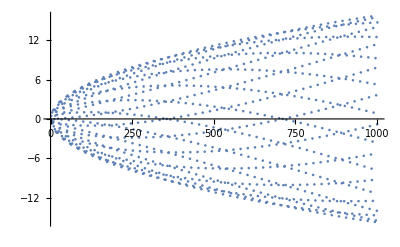

```mathematica
$TextStyle={FontSize->14}
lst=Table[Sqrt[n]Sin[n]Cos[n],{n,0,1000}]
p8=ListPlot[lst]
```

Получив в качестве аргумента список числовых пар (двухэлементных списков), команда ListPlot изобразит точки с соответствующими парами координат.

{{-3,Cos[3]},{-5/2,Cos[5/2]},{-2,Cos[2]},{-3/2,Cos[3/2]},{-1,Cos[1]},{-1/2,Cos[1/2]},{0,1},{1/2,Cos[1/2]},{1,Cos[1]},{3/2,Cos[3/2]},{2,Cos[2]},{5/2,Cos[5/2]},{3,Cos[3]}}

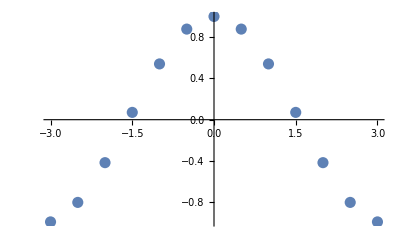

```mathematica
lst1=Table[{i,Cos[i]},{i,-3,3,1/2}]
p9=ListPlot[lst1,PlotStyle->PointSize[0.02]]
```

Опция PlotStyle в данном случае используется для установления размера выводимых точек в 2% от общей ширины рисунка.

Команды Plot, ParametricPlot, ParametricPlot3D позволяют выводить на одном рисунке графики нескольких функций одновременно. Для совмещения рисунков, полученных этими, а также и другими графическими командами, используется команда Show.

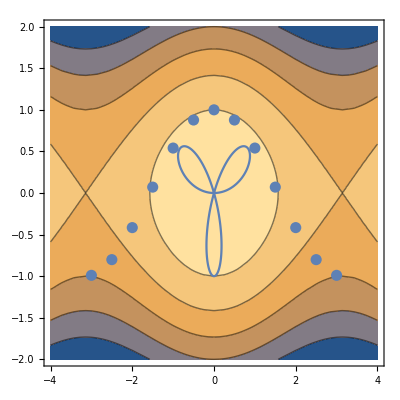

```mathematica
Show[p7,p4,p9]
```

Изображения перекрывают друг друга в том же порядке, в каком перечисляются соответствующие переменные.

### Задача 18.

Построить совместные графики функций f(x)=5 x^4-12 x^3+8 x^2+2  и её производной на интервале (-1,2). Сравните интервалы убывания и возрастания функции со знаком производной.

Решение:

```mathematica
D[5 x^4-12 x^3+8 x^2+2,x]
```

16 x-36 x^2+20 x^3

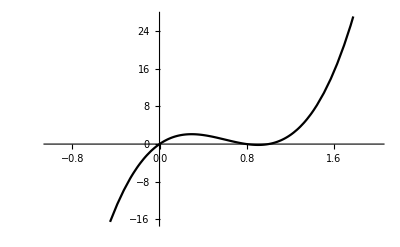

```mathematica
Plot[
{5 x^4-12 x^3+8 x^2+2,
16 x-36 x^2+20 x^3},
{x,-1,2},PlotStyle->{RGBColor[25,47,194],RGBColor[0,0,0]}]
```

### 1.11 Команды решения уравнений

Для компьютерной алгебраической системы наряду с возможностями преобразования символьных выражений не менее важным является умение решать уравнения. В Mathematica наиболее часто для этих целей используется команда Solve:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Первым аргументом записывается решаемое уравнение (или список уравнений в случае решения системы), второй аргумент — переменная (или список переменных), относительно которой требуется найти решение. Отметим, что при записи уравнения используется двойной знак равенства (инфиксная форма оператора Equal). Найденное решение представляется в виде двумерного списка правил подстановок, которым можно легко воспользоваться в дальнейших вычислениях.

```mathematica
x/.%
```

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

В случае решения уравнения с одной символьной переменной второй аргумент может не указываться:

```mathematica
Solve[4 x^3+6 x^2+3x-4==0]
```

{{x→1/2 (-1+3^(2/3))},{x→-1/2-1/4 3^(2/3) (1-ⅈ √3)},{x→-1/2-1/4 3^(2/3) (1+ⅈ √3)}}

Команда Solve позволяет получить точное решение любого полиномиального уравнения до четвертой степени включительно и некоторых других.

```mathematica
Solve[2 x^20+ x^12==0]
```

{{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→-(-1/2)^(1/8)},{x→(-1/2)^(1/8)},{x→-(-1)^(3/8)/2^(1/8)},{x→(-1)^(3/8)/2^(1/8)},{x→-(-1)^(5/8)/2^(1/8)},{x→(-1)^(5/8)/2^(1/8)},{x→-(-1)^(7/8)/2^(1/8)},{x→(-1)^(7/8)/2^(1/8)}}

Для полиномиального уравнения, точное алгебраическое решение которого получить нельзя, команда Solve возвратит решение следующего вида:

```mathematica
equ1=x^5+x^4+2x^3-x^2+4x+3==0
sols=Solve[equ1,x]
```

3+4 x-x^2+2 x^3+x^4+x^5==0

{{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,1]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,3]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,4]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,5]}}

Ограничимся лишь замечанием, что с каждым из полученных таким образом корней можно работать, как с точным числовым значением.

```mathematica
Expand[(Part[x/.sols,2]+b)^2]
```

b^2+2 b Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]+Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]^2

Получить приближенное значение этих корней с любой точностью также не составляет труда.

```mathematica
N[sols]
```

{{x→-0.58013},{x→-0.992048-1.51736 ⅈ},{x→-0.992048+1.51736 ⅈ},{x→0.782113-0.980699 ⅈ},{x→0.782113+0.980699 ⅈ}}

### Задача 6.

Найти решения системы уравнений x^2+y^2=1,x-y=1/2.

Решение:

```mathematica
Solve[{x^2+y^2==1,x-y==1/2},{x,y}]
```

{{x→1/4 (1-√7),y→1/4 (-1-√7)},{x→1/4 (1+√7),y→1/4 (-1+√7)}}

### Задача 11.

Решить уравнение x^3-2x+1=0.

Условие задачи — назначение функции Solve. Функция Solve будет пытаться решать уравнение в символьном виде. Напомним,что для системы Mathematica числа

2/3,√2

и тому подобные выражения, cоставленные из целых чисел, являются символами. Поэтому решения, получаемые функцией  Solve, подчас являются излишне громоздкими. Для того, чтобы просто численно решить уравнение с необходимым числом знаков после запятой, используется функция NSolve. Впрочем от решений, полученных функцией Solve, легко перейти к решениям, полученным функцией NSolve, но не наоборот.

```mathematica
Clear[x]
```

```mathematica
Solve[x^3-2x+1==0,x]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
NSolve[x^3-2x+1==0,x]
```

{{x→-1.61803},{x→0.618034},{x→1.}}

График многочлена

x^3-2x+1

можно использовать для того, чтобы найти решения графическим способом и сравнить с полученными.

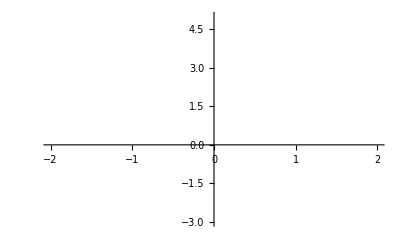

```mathematica
Plot[x^3-2x+1,{x,-2,2},
PlotStyle ->{RGBColor[13, 1, 171]}]
```

### Задача 12.

Решить уравнение a x^2+b x+c=0 относительно параметров a, b, c.

Здесь ситуация несколько иная, чем в задаче 11. Необходимо проанализировать все варианты взаимного расположения параметров a,b и c. С этим успешно справляется функция Reduce (см.описание в Help).

```mathematica
Clear[x,a,b,c]
```

```mathematica
Reduce[a x^2+b x+c==0,a]
Reduce[a x^2+b x+c==0,b]
Reduce[a x^2+b x+c==0,c]
```

(x==0&&c==0)||(x≠0&&a==(-c-b x)/x^2)

(x==0&&c==0)||(x≠0&&b==(-c-a x^2)/x)

c==-b x-a x^2

Булевы операции конъюнкции И (&&)и дизъюнкции ИЛИ (||), а также двуместные РАВНО (==) и НЕ РАВНО (≠) вполне понятны без дополнительных разъяснений и вывод результата работы функции Reduce легко интерпретируется.

### Задача 14.

Решить уравнение x^4+2 x^3-6 x^2+2x+1=0.

То же самое, что и в задаче 11. Можно только подметить, что многочлен обладает специальным свойством, поэтому существует изящный математический алгоритм решения предложенного уравнения. Этот алгоритм также может быть реализован средствами системы Mathematica.

Сначала найдем решение непосредственно, используя функцию Solve.

```mathematica
Clear[x,eqns,f,sol]
```

```mathematica
eqns=x^4+2 x^3-6 x^2+2x+1
```

1+2 x-6 x^2+2 x^3+x^4

```mathematica
Solve[eqns==0,x]
```

{{x→1},{x→1},{x→-2-√3},{x→-2+√3}}

Теперь заметим, что функция f(x) удовлетворяет следующему условию :

f(1/x)x^4=f(x).

Действительно,

```mathematica
f[x_]=x^4+2 x^3-6 x^2+2x+1
```

1+2 x-6 x^2+2 x^3+x^4

```mathematica
FullSimplify[f[1/x] x^4==f[x]]
```

True

Воспользуемся этим, чтобы найти решения другим способом.

```mathematica
sol=Flatten[Solve[Simplify[Expand[eqns/x^2],x+1/x==y]==0,y]]
```

{y→-4,y→2}

```mathematica
Solve[x+1/x==sol[[2]][[2]],x]
```

{{x→1},{x→1}}

```mathematica
Solve[x+1/x==sol[[1]][[2]],x]
```

{{x→-2-√3},{x→-2+√3}}

Смысл второго способа решения возвратных уравнений в том, что он позволяет находить в квадратурах решения возвратных уравнений, если их степень не превышает 8. Функция Solve решить возвратное уравнеие степени выше 4 в квадратурах не сможет, поскольку она не различает внутреннюю структуру многочлена. Этот пример, в частности, подтверждает тот очевидный факт, что никакая система компьютерной алгебры не в состоянии заменить профессионально подготовленного специалиста. А вот для специалиста она может стать незаменимым помощником.

### Задача 15.

Выяснить, является ли многочлен  x^4+4 x^3-2 x^2-12x+9 точным квадратом, т.е. можно ли подобрать три числа p, q, r так, чтобы имело место тождество x^4+4 x^3-2 x^2-12x+9=(p x^2+q x+r)^2.

Решение:

```mathematica
Clear[x,p,q,r,a,b,c,d,f]
```

```mathematica
Factor[x^4+4 x^3-2 x^2-12x+9]
```

(-1+x)^2 (3+x)^2

Данный многочлен является полным квадратом cо следующими коэффициентами p, q, r:

```mathematica
SolveAlways[x^4+4 x^3-2 x^2-12x+9==(p x^2+q x+r)^2,x]
```

{{p→-1,r→3,q→-2},{p→1,r→-3,q→2}}

А теперь в общем случае:

```mathematica
SolveAlways[a x^4+b x^3+c x^2+d x+f==(p x^2+q x+r)^2,x]
```

{{a→p^2,b→2 p q,c→q^2+2 p r,d→2 q r,f→r^2}}

Функция SolveAlways находит соотношения между одной группой переменных (в данном случае p,q,r,a,b,c,d,f) при условии, что равенство выполняется для всех значений другой группы переменных (в данном случае x).

### Задача 16.

Показать, что многочлен x^2+y^2+z^2 нельзя представить в виде произведения (ax+by+cz)(Ax+By+Cz) ни при каких вещественных или комплексных числах a,b,c,A,B,C.

Решение:

```mathematica
SolveAlways[x^2+y^2+z^2==(a x+b y+c z)(A x+B y+C z),{x,y,z}]
```

Проверим, что действительно получается пустое множество решений

```mathematica
Collect[Expand[x^2+y^2+z^2-(a x+b y+c z)(A x+B y+C z)],x]
```

```mathematica
lst=CoefficientList[Expand[x^2+y^2+z^2-(a x+b y+c z)(A x+B y+C z)],x]
```

Получаем систему уравнений

```mathematica
ur=(#==0)&/@lst
```

```mathematica
Solve[ur,{a,b,c}]
```

Данная система уравнений не имеет решений, а значит не существует требуемого представления.

Однако для нахождения численного решения уравнения существуют и специализированные средства.

Команда NSolve находит численно все решения полиномиального уравнения или системы таких уравнений.

```mathematica
NSolve[equ1,x]
```

{{x→-0.992048-1.51736 ⅈ},{x→-0.992048+1.51736 ⅈ},{x→-0.58013},{x→0.782113-0.980699 ⅈ},{x→0.782113+0.980699 ⅈ}}

Третьим аргументом этой команды может указываться число, соответствующее количеству числовых знаков в получаемом результате.

Если в решении уравнения не помогают ни Solve, ни NSolve можно воспользоваться функцией численного отыскания корня FindRoot. Используя метод Ньютона, эта функция находит один из корней уравнения по заданному начальному приближению.

```mathematica
FindRoot[Cos[Log[x]]-Sin[x/2],{x,1}]
FindRoot[Cos[Log[x]]-Sin[x/2],{x,0.5}]
```

{x→1.87954}

{x→0.233639}

В NSolve и FindRoot первым аргументом может быть не только уравнение (в отличие от Solve), но и функция, корни которой необходимо найти.

Для решения полиномиальных уравнений может быть использована и функция Roots, которая действует аналогично Solve, но позволяет получить результат в иной форме.

```mathematica
Roots[x^3+3x^2-x-6==0,x]
```

x==1/2 (-1-√13)||x==1/2 (-1+√13)||x==-2

Решение записывается в виде выражения, результатом которого после подстановки конкретного значения x будет одна из встроенных логических констант — True (истина) или False (ложь). В данном случае связка логических операций записана с использованием уже знакомой нам команды Equal (которая может использоваться не только для записи уравнений, но и как самостоятельная логическая команда для сравнения двух числовых величин) и команды Or (инфиксная форма ||). Отметим, что Or (логическое или) имеет более низкий приоритет по сравнению с Equal. Результат True, как легко догадаться, получится только в случае, когда в качестве значения x будет подставлен один из корней уравнения.

```mathematica
%/.x->-2
```

True

Команда Roots в сочетании с командой ToRules позволяет получить решения уравнения в виде более привычного двумерного списка правил подстановок.

```mathematica
{ToRules[%%]}
```

{{x→1/2 (-1-√13)},{x→1/2 (-1+√13)},{x→-2}}

### 1.12 Выражения и переменные

Ранее мы уже пользовались различными переменными, обозначая ими результаты выполненных команд, которые могли потребоваться в дальнейшей работе. При этом набор символов, используемый как переменная, мог обозначать и символьное выражение, и целое уравнение, и даже график функции: пользователю не надо заботиться об объявлении переменной того или иного типа и следить за резервированием для нее памяти.

Отдельные числа или символы, уравнения и графики и т. п. — все эти объекты являются выражениями Mathematica, для которых предусмотрены единые правила записи. Одни выражения строятся посредством комбинирования других, более мелких. Наиболее мелкие (атомарные) выражения в Mathematica — это числа (целые, вещественные, рациональные или комплексные), символы и строки.

Рассмотрим, например, четыре числа: целое, вещественное (т.е. в терминологии Mathematica — с десятичной точкой), рациональное и комплексное.

```mathematica
FullForm[34]
FullForm[66.8]
FullForm[2/3]
FullForm[1+I]
```

34

66.8

Rational[2,3]

Complex[1,1]

Команда FullForm отображает стандартную форму представления выражений в Mathematica (далеко не все команды используются в стандартной форме, и, например, знак "+" — инфиксная форма команды Plus — не относится к стандартной записи операции сложения). Полученные результаты говорят о том, что рациональные и комплексные числа имеют в Mathematica несколько иное представление, нежели целые и вещественные. И хотя числа всех этих четырех типов считаются атомарными выражениями, для описания рациональных и комплексных явным образом используются заголовки: эти типы описываются "командами" Rational и Complex соответственно. Альтернативные варианты ввода таких чисел — с помощью наклонной черты "/" и константы I — реализованы для удобства. Поскольку в Mathematica любая команда с двумя аргументами f[expr1, expr2] может быть записана в инфиксной форме

expr1~f~expr2,

то, вообще говоря, для определения рациональной дроби возможна также следующая не очень удобная конструкция:

```mathematica
2~Rational~3
```

2/3

Атомарное выражение "символ" — это любая последовательность букв (напомним, что Mathematica различает строчные и прописные буквы), цифр и знака $. Символ не может начинаться с цифры — такая запись интерпретируется как умножение этой цифры на символ из остальных знаков. Во многих приведенных выше примерах различные символы использовались в качестве идентификаторов переменных.

Еще один тип атомарного выражения — "строка" — это последовательность ASCII-символов, заключенная в кавычки.

Команда FullForm, примененная к произвольным символам и строкам, как и следовало ожидать, не дает никакого раскрытия их внутренней структуры.

```mathematica
FullForm[x1]
FullForm[f2RT$s]
FullForm["This is a string"]
FullForm["строка"]
```

x1

f2RT$s

"This is a string"

"\:0441\:0442\:0440\:043e\:043a\:0430"

В Mathematica всякое выражение либо является атомарным, либо имеет следующую структуру f[a_1,a_2,...,a_n],где

a_1,a_2,...,a_n  — выражения Mathematica,n — длина выражения. Заголовок f может быть выделен из выражения командой Head.

```mathematica
expr=(a+b*c)^2-Sin[d-e/f]
FullForm[expr]
Head[expr]
```

(a+b c)^2-Sin[d-e/f]

Plus[Power[Plus[a,Times[b,c]],2],Times[-1,Sin[Plus[d,Times[-1,e,Power[f,-1]]]]]]

Plus

Доступ к элементам  осуществляется с помощью команды Part.

```mathematica
Part[expr,1]
expr[[2]]
```

(a+b c)^2

-Sin[d-e/f]

Количество структурных элементов  (длина выражения) может быть определено командой Length.

```mathematica
Length[expr]
```

2

Каждый из элементов выражения сам является выражением, имеет заголовок и может быть разделен на структурные части. Такое выделение структурных частей можно продолжать до получения только атомарных выражений.

```mathematica
expr[[2,2,1,2,3,1]]
```

f

Атомарные выражения имеют только заголовки — Integer, Real, Symbol, String. Рациональные и комплексные числа представляют собой особые атомарные выражения: в своем представлении они имеют и заголовок, и структурные части, но команды Part[expr, 1] или Part[expr, 2] к выражениям с заголовками Rational и Complex не применяются.

Заголовок любого выражения expr считается его нулевым структурным элементом, поэтому аналогом команды Head[expr] служит команда Part[expr, 0] (или expr[[0]]).

Существует способ искусственно добавить к ряду выражений один и тот же заголовок. Для этого используется команда Map (краткая инфиксная форма — /@), первый аргумент которой — выражение, выполняющее роль заголовка, второй — преобразуемое выражение или список выражений.

```mathematica
Map[ddd,{a,b,c,d}]
```

{ddd[a],ddd[b],ddd[c],ddd[d]}

В случае, когда первый аргумент является наименованием какой-либо функции, такая операция автоматически приводит к применению этой функции ко второму аргументу или (в случае списка) к каждому его элементу.

```mathematica
Length/@
{Sin[x^2-y],a+b,Solve[x^2+x-4==0,x]}
```

{1,2,2}

Итак, переменной (как правило, атомарным символом) может быть обозначено всякое выражение. Производится эта операция с помощью команды немедленного присвоения Set[expr1, expr2] (=). В этом случае вычисление второго элемента выражения (правой части в записи присвоения) производится немедленно и результат присваивается первому элементу. Если же необходимо присвоить переменной не результат, а исходное значение выражения, то используется команда отложенного присвоения Set-

Delayed[expr1, expr2] (:=).

В следующем примере значение переменной a — псевдослучайное вещественное число из интервала [0,1] , а значение переменной b — команда, вычисляющая псевдослучайное число заново всякий раз, когда в вычислениях используется символ b.

```mathematica
a=Random[]
```

0.915136

```mathematica
b:=Random[]
```

```mathematica
a-a
b-b
```

0.

0.424119

Для освобождения переменной от значения служит команда Clear.

```mathematica
Clear[a,b]
a
b
```

a

b

В Mathematica существует также несколько специальных команд для изменения значений числовых переменных.

```mathematica
{a=1,a++,a}
```

{1,1,2}

```mathematica
{b=1,++b,b}
```

{1,2,2}

```mathematica
{c=3,c*=4,c}
```

{3,12,12}

### Задача 7.

Упростить логическое выражение
(¬x∧¬y∧¬z)∨(x∧y∧z)∨(x∧¬y∧z)∨(¬x∧¬y∧z)∨(¬x∧y∧z)∨(¬x∧y∧¬z).

Функция LogicalExpand непосредственно решает,рассматриваемую задачу.Это ее назначение применения (см.Help).

```mathematica
LogicalExpand[!x&&!y&&!z||x&&y&&z||x&&!y&&z||!x&&!y&&z||!x&&y&&z||!x&&y&&!z]
```

z||!x

Команды

Increment[var] (var++),
PreIncrement[var] (++var),
Decrement[var] (var--),
PreDecrement[var] (--var),
AddTo[var, number] (var += number),
TimesBy[var, number] (var = number)

и некоторые другие служат для оперативного изменения значений числовых переменных в процессе выполнения более сложных вычислений.